# Atom-field interactions: semiclassical models

```mathematica
<<Wolfram`QuantumFramework`

creationAnnihilation[n_]:=Module[{ca,aa},
aa=QuantumOperator[SparseArray[Band[{1,2}]->√Range[n-1],{n,n}],n];
ca=aa["Dagger"];
{aa,ca}]

fockN[n_,d_]:= QuantumState[SparseArray[{n+1 -> 1}, d], d]
atomBasis = QuantumBasis[QuditBasis[{"a","b"}]];
```

The starting point to understand atom-field interactions is to study the coupling of a single mode field and two level atom. In the semiclassical model the atom is quantized and the field is treated as a classical field. Using dipole approximation when field wavelength is larger than atomic size, the mathematics are analogous to a spin 1/2 particle. In the same manner as a spin 1/2 particle have Rabi oscillations when interacting with a time dependent magnetic field, the two level atom shows optical Rabi oscillations.

## Atom-field interaction processes

### Absorption

If we consider an atom with levels |a⟩, |b⟩, |c⟩...  with energies E_A , E_(B,)E_(C ...) being the level |a⟩ being the lowest energy level. And a electric field 
E(r, t) = E_0 cos(ω t + ϕ (r)). Absorption consists of an atom in a particular state goes to a higher energy level and in the process the amplitude of the electric field reduces. This is relevant when the field frequency is quasi-resonant  that is  ω ≃ ω_ba = (E_b-E_a)/h, for ω close to that frequency the model can be simplified to just a two level atom.

### Stimulated emission

Stimulated emission is the process that is in a way opposite to absorption but is also relevant when the field frequency is quasi-resonant, in this case an atom decays to a lower energy level and the field is amplified. For the field to be amplified means that a photon was emitted with the same frequency as the incident field , and also has the same polarization and phase so they can interfere coherently.

### Spontaneous emission

Even when there is not a an electromagnetic field an atom can also decay from state |b⟩ to  |a⟩, and a photon is emitted at the resonant frequency. The emitted photon leaves the atom with completely arbitrary phase and polarization. This phenomenon is introduced in this section for the sake of completeness, but cannot be explained until we consider interactions of an atom with a quantized field (all the modes including the vacuum).

NOTE: in the diagrams we are depicting photons because make the diagrams clearer, but the field considered will be classical

## Semiclassical Hamiltonian models

The simplest model that is semiclassical is to consider , the dynamics of a single electron in the field of a stationary nucleus. The motion of the electron is described by quantum operators, while the field is taken to be classical defined by the potentials A(r,t) and U(r,t)
It can be shown using the Lagrangian formalism that the interaction Hamiltonian that include the field of the nucleus, and also external fields takes the following form:

this Hamiltonian leads to the classical equation of motion when averages  values are calculated
There exists an infinite number of pairs {A(r,t), U(r,t)} associated with values of electric and magnetic fields, going from a pair of potentials to another valid pair is done by the so called Gauge transformations


where F(r,t)  is just a scalar field

### Coulomb gauge and A · p Hamiltonian

It is known that there are infinite solutions { A(r,t) and U(r,t) } that reproduce an electromagnetic field related by Gauge transformations. Additional conditions on the potentials determine a choose of a Gauge that removes the arbitrariness . One choice that is used a lot in quantum optics, is the Coulomb Gauge determined by the condition:

This choice for the vector potential is called  the transverse vector potential A_⊥(r,t ), for example in the case of plane electromagnetic wave
the Coulomb Gauge potentials A_⊥= -E_0/ωsin(ω t-k·r)     and  U(r,t) = 0  reproduce the E and B fields for this case.
And the electric field is related to the vector potentials as

E(r,t) = - ∂/(∂t) A_⊥(r, t)

When analyzing the interaction of an electron evolving in an external applied field and the Coulomb potential of the nucleus. If we take the external field to be a plane wave, the nuclear electrostatic field has zero vector potential and the scalar potential is  V_coul(r) = q U_coul(r). Then the semiclassical interaction Hamiltonian is

Expanding the terms 

After simplifying using the Gauge condition we can distinguish two parts, H_0 is just related to a charged particle moving in a Coulomb nuclear field and H_I is the interaction term of the external field and the hydrogen-like atom


In atom-light interactions the wavelength λ  of the light is typically  very large compared to the atomic size. The amplitude of the external field is approximated constant along the atom A_⊥(r_0, t) it is well known as a long-wavelength approximation
In this approximation the vector potential is just a constant 
(Ĥ)_I = -q/m p· A_⊥(r_0,t)+q^2/(2m)(A^2)_⊥(r_0 , t) 
The second term have matrix element between different atomic states equal to 0 , so atomic transitions are not possible, therefore the interaction Hamiltonian can be written just as:
(Ĥ)_I = -q/mp̂ · A_⊥(r_0, t)
This Hamiltonian  the “p ·A  Hamiltonian”  uses the  Coulomb Gauge to specify a vector potential taken at the position of the nucleus

### Göppert-Mayer Gauge and electric dipole Hamiltonian

The Göppert-Mayer Gauge is obtained by doing a Gauge transformation to the Coulomb Gauge with the following scalar field that gives s:
F(r,t) = - (r - r_0) · A_⊥(r_0,t)
This transformation changes the potentials to :

 
With these potentials the Hamiltonian becomes:

Using  the relation between the electric field and vector potential and introducing the operator D̂= q(r̂-r_0) the Hamiltonian can be rewritten as:

For this case we can also use the long-wavelength approximation replacing A'(r̂,t) by A'(r_0,t) using the transformed potentials we get
A'(r_0,t) = 0 and finally the Hamiltonian terms  become


This form is referred as the electric dipole Hamiltonian , because it has the form of interaction energy of a classical electric dipole located at r_0 with an electric field E

Even if we have two different Hamiltonians , if we use exact equations and do not employ any additional approximation the predictions are the same regardless of the Hamiltonian choice . The long-wavelength approximation also predicts the same transition probabilities independent if A · p or D ·E is used . However, if extra approximations are used the results can differ depending on the specific problem, one Hamiltonian can provide more  accurate results to certain problems.

## Atomic transitions: Rabi oscillations

We already described how to get an interaction Hamiltonian in the semiclassical theory, so now we can study the transitions between atomic levels when a sinusoidally oscillating electromagnetic wave using first-order perturbation theory, and a more exact method using a two level atom in the quasi-resonant approximation

### Transition probabilities in first-order perturbation theory

Given a system describing an atom with Hamiltonian H_0 with eigenstates |j⟩ associated with energy levels E_j . Also the atom is initially in the eigenstate |i⟩ of H_0 and the external electromagnetic field has frequency ω , a problem is to find the probabilities that the atom is in a different eigenstate |k⟩ at a later time t. We assume that the validity of the usage of the interaction Hamiltonians can be extended to other atoms and not just hydrogen, so we assume we can use the long-wavelength approximation electric dipole Hamiltonian
(Ĥ)_I = -D̂ · E(r_0,t) where D̂ has non zero matrix element between different eigenstates of H_0. Using the classical expression for an electric field we can write
OverHat[H_I] (t) =Ŵ cos(ωt + ϕ) where Ŵ = D̂ · E(r_0)

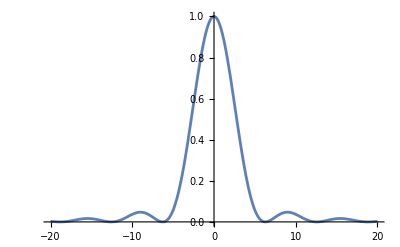

```mathematica
Plot[T^2(Sinc[δ T/2])^2 /. T->1,{δ,-20,20}]
```

### Rabi oscillations between two levels